```mathematica
ClearAll["Global`*"]
```

## Import Data

```mathematica
task=2; (* 1 for protest; 2 for mass shooting *)

If[task==1,
data0=Import[StringJoin[NotebookDirectory[],"2a - analysis - Count Love.xlsx"]],
data0=Import[StringJoin[NotebookDirectory[],"2b - analysis - MST 2013 - 2018.xlsx"]]]

(* first column is data: 1900/1/1 is 1 *)
```

{{{43281.,Jersey City,0.,5.,,HudsonCounty,NewJersey,40.7114,-74.0648,1.},{43280.,Ashburn,0.,8.,,TurnerCounty,Georgia,31.7092,-83.6524,1.},2132,{41275.,McKeesport,0.,4.,,AlleghenyCounty,Pennsylvania,40.3419,-79.845,1.},{41275.,Sacramento,2.,3.,,SacramentoCounty,California,38.5666,-121.469,1.}}}
 |  |  |  |

## Data Selection and Cleaning

```mathematica
(* select some data only; remove selection column *)
{{xMin,xMax},{yMin,yMax}}={{-130,-65},{25,50}}(*{{-170,-65},{25,70}}*);

data1=First@data0;
data1=Select[data1,#[[-1]]==1&];

data1=Drop[data1,None,{-1}]

data1=Select[data1,And[yMin<=#[[-2]]≤yMax,xMin<=#[[-1]]≤xMax]&];

(* remove cases with location N/A *)
data1=Select[data1,#[[-1]]≠"Failure"&];

(* filter out old dates *)
msAdj=1; (* Microsoft Excel mistaken let 1900/2/29 exist,which shouldn't *)
dateFilter=First@DateDifference[DateObject[{1900, 1, 1}],DateObject[{2017, 3, 3}]]+1+msAdj;
data1=Select[data1,#[[1]]>=dateFilter&];
firstdate=Min@data1[[All,1]];
firstdateD=DateObject[{1900, 1, 1}]+Quantity[firstdate-1-msAdj,"Days"]

(*scale filtering*)
scaleFilter=5;
If[task==1,Nothing,data1=Select[data1,#[[3]]≥scaleFilter&]];
```

{{43281.,Jersey City,0.,5.,,HudsonCounty,NewJersey,40.7114,-74.0648},{43280.,Ashburn,0.,8.,,TurnerCounty,Georgia,31.7092,-83.6524},{43279.,Annapolis,5.,0.,,AnneArundelCounty,Maryland,38.9723,-76.5064},2128,{41275.,McKeesport,0.,4.,,AlleghenyCounty,Pennsylvania,40.3419,-79.845},{41275.,Sacramento,2.,3.,,SacramentoCounty,California,38.5666,-121.469}}
 |  |  |  |

Day: Fri 3 Mar 2017

```mathematica
(* update 50k to 50,000 *)
times1000[s_]:=If[NumericQ[s],s,If[StringTake[s,-1]=="k",ToExpression[StringDrop[s,-1]]*1000,s]];
logtimes1000[s_]:=If[NumericQ[s],Log[s],If[StringTake[s,-1]=="k",Log[ToExpression[StringDrop[s,-1]]*1000],s]];
pplSize=times1000/@data1[[All,3]];
data1[[All,3]]=pplSize;
Take[data1,10]

(* Delete Duplicate *)
data1=SortBy[data1,{-#[[1]],-#[[3]]}&];
data1=DeleteDuplicatesBy[data1,#[[{1,-2,-1}]]&];
```

{{43279.,Annapolis,5.,0.,,AnneArundelCounty,Maryland,38.9723,-76.5064},{43262.,Orlando ,5.,1.,,OrangeCounty,Florida,28.5335,-81.3758},{43238.,Sante Fe,10.,13.,,UnknownEntity,Texas,31.4818,-99.3701},{43236.,Ponder,5.,1.,,DentonCounty,Texas,33.1717,-97.2965},{43157.,Detroit,5.,0.,,WayneCounty,Michigan,42.383,-83.1022},{43145.,Parkland,17.,17.,,BrowardCounty,Florida,26.3151,-80.2472},{43141.,Paintsville,5.,0.,,JohnsonCounty,Kentucky,37.812,-82.8042},{43128.,Melcroft,5.,0.,,UnknownEntity,Pennsylvania,40.8758,-77.8023},{43053.,Corning,6.,12.,,TehamaCounty,California,39.9282,-122.182},{43044.,Sutherland Springs,27.,20.,,UnknownEntity,Texas,31.4818,-99.3701}}

## Clustering

```mathematica
(* rescaling *)
(* Do Clustering *)

nStart=1;
nEnd=Length[data1]; (* or smaller; all = 6077*)

scaleTime1=175; (* justified in "0.2 - counties distance.nb" *)

nCts=Automatic;

(* created data2 = rescaled(data1)  *)
data2=MapAt[(#-firstdate)/365*scaleTime1&,data1,{All,1}];

(*data2[[All,1]]=data2[[All,1]]*scaleTime1;*)
{t,cts}=Timing@FindClusters[data2[[nStart;;nEnd,{1,-2,-1}]]->data2[[nStart;;nEnd]],nCts,DistanceFunction->EuclideanDistance];
 t

(* {t,cts}=Timing@FindClusters[data2[[nStart;;nEnd,{1,-2,-1}]]->data2[[nStart;;nEnd]],DistanceFunction->EuclideanDistance,Method->"Agglomerate"] *)
(* {t,cts}=Timing@FindClusters[data2[[nStart;;nEnd,{1,-2,-1}]]->data2[[nStart;;nEnd]],nCts,CriterionFunction->"CalinskiHarabasz"] *)
(*data2[[All,1]]=data2[[All,1]]/scaleTime1;*)

n=Length[cts]
```

0.171875

5

## Plotting

```mathematica
(* create the image of Geo Map *)

yManualAdj=0;

g1=(GeoPosition[{yMin+yManualAdj,#}]&/@Range[xMin,xMax,5]);
g2=(GeoPosition[{yMax+yManualAdj,#}]&/@Range[xMax,xMin,-5]);
img=Lighter@GeoGraphics[Polygon@Join[g1,g2],GeoProjection->"CylindricalEqualArea",GeoRangePadding->None];
```

```mathematica
(* year adj*)
MaxTimeD=DateObject[{2018,6,30}];
MaxTime=N@(First@DateDifference[firstdateD,MaxTimeD])*scaleTime1/365;

ctsSel=cts[[All,All,{-1,-2,1}]];
plotRange1={{xMin,xMax},{yMin,yMax},{0,MaxTime}};
boxRatios1={1.2,0.7,2};
slices={0,0.721,0.778,0.798,0.855,1}*MaxTime; 
 slicesB={0,MaxTime}; 
colCts=ColorData[97]/@Range[n];
timetick1=Table[{n,DateString[firstdateD+Quantity[n/scaleTime1,"Years"],{"Month","/","Day","/","YearShort"}]},{n,slices}]; (* 100 unit = 1 year *)

plot1=Plot3D[Drop[slices,-1],{x,xMin,xMax},{y,yMin,yMax},PlotRange->plotRange1,Ticks->{Automatic,Automatic,timetick1},BoxRatios->boxRatios1,PlotStyle->Texture[img]];
plot1B=Plot3D[Drop[slicesB,-1],{x,xMin,xMax},{y,yMin,yMax},PlotRange->plotRange1,Ticks->{Automatic,Automatic,timetick1},BoxRatios->boxRatios1,PlotStyle->Texture[img]];
plot2=ListPointPlot3D[ctsSel,PlotRange->plotRange1,Ticks->{Automatic,Automatic,timetick1},BoxRatios->boxRatios1];
plot3=Table[{HighlightMesh[ConvexHullMesh[ctsSel[[i]]],Style[2,colCts[[i]],Opacity[0.5]]]},{i,n}];

Show[{plot1B,plot2},ViewPoint->{-0.4,-1.1,2.3}]
Show[{plot1,plot2}]
Show[{plot1B,plot2,plot3}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
BubbleChart3D@cts[[All,All,{-1,-2,1,3}]]
```

-Graphics3D-

```mathematica
plot4=Graphics3D[{Transpose[{colCts,Point/@ctsSel}],Opacity[0.25],Transpose[{colCts,BoundingRegion[#,"FastEllipsoid"]&/@ctsSel}]}];

Show[{plot1B,plot4}]
```

-Graphics3D-

## Graph

```mathematica
IGMeshGraph[mesh_]:=Graph[Range@MeshCellCount[mesh,0],MeshCells[mesh,1][[All,1]],EdgeWeight->PropertyValue[{mesh,1},MeshCellMeasure],VertexCoordinates->MeshCoordinates[mesh],PlotTheme->"Default"];
f[{p_,q_}]:=Sqrt[p^2+q^2];

plot5All=nAllJ=statEdgeVecAllJ=corrEdgeVecAllJ=lambdasAllJ=ctsSelAllJλ=scaleGrowthAllJ={};

(*** diffussion analysis ***)

 For[j=1,j≤n,j++, (* select cluster *)

(* create tree of the cluster *)

ctsSelJ=ctsSel[[j]];

graph=IGMeshGraph@DelaunayMesh[ctsSelJ];
plot5=FindSpanningTree[graph,VertexCoordinates->GraphEmbedding@graph,EdgeShapeFunction->"Line",EdgeStyle->{Thick,Black},VertexSize->Tiny,VertexStyle->Black,PlotTheme->"Default"];
plot5All=Append[plot5All,plot5];

nJ=VertexCount[plot5];
nAllJ=Append[nAllJ,nJ];

vtxCood=PropertyValue[plot5,VertexCoordinates];

(*** Edges Analysis ***)

edges=EdgeList[plot5];

(* edgeVectors = {combining Δlat and Δlong, Δtime} *)
edgeVectors=Table[vtxDiff=vtxCood[[edges[[n,1]]]]-vtxCood[[edges[[n,2]]]];{f[vtxDiff[[1;;2]]],Abs@vtxDiff[[3]]},{n,1,Length@edges}];

(* jump statistic *)
statEdge=Table[#@edgeVectors[[All,i]]&/@{Mean,StandardDeviation,Quantile[#,{1/4,1/2,3/4}]&},{i,1,2}];
statEdgeVecAllJ=Append[statEdgeVecAllJ,statEdge];

(* deg-time correlation *)
corrEdge=Correlation@edgeVectors;
corrEdgeVecAllJ=Append[corrEdgeVecAllJ,corrEdge[[1,2]]];

(* Gamma Distribution Modeling *)
distml=Table[EstimatedDistribution[edgeVectors[[All,i]],ExponentialDistribution[λ]],{i,1,2}];
{λ1,λ2}=1/Mean/@distml;
lambdasAllJ=Append[lambdasAllJ,{λ1,λ2}];

ctsSelJλ=ArrayFlatten[{{ctsSelJ,ConstantArray[{λ1,λ2,λ1*λ2},nJ]}}];
ctsSelAllJλ=Append[ctsSelAllJλ,ctsSelJλ];

(*** Study expected growth of scale; weight = log(scale) ***)

vtxScale=cts[[j]][[All,3]];

ratioVectors1=Table[
vtx1=edges[[n,1]];
vtx2=edges[[n,2]];
If[Or[vtxScale[[vtx1]]=="---",vtxScale[[vtx2]]=="---",vtxCood[[vtx1,3]]==vtxCood[[vtx2,3]]],
"---",
(vtxScale[[vtx1]]/vtxScale[[vtx2]])^-Order[vtxCood[[vtx1,3]],vtxCood[[vtx2,3]]]
]
,{n,1,Length@edges}];

scaleGrowthKnown=Exp@N@Mean@Log@Select[ratioVectors1,#≠"---"&];
scaleGrowthAllJ=Append[scaleGrowthAllJ,scaleGrowthKnown];

]
```

TetGenLink`TetGenDelaunay::tetfc: A Delaunay tetrahedralization could not be found from the points {{-106.103,34.4274,49.863},{-81.3758,28.5335,45.0685},{-88.9201,32.8298,40.7534}}.

Range::range: Range specification in Range[MeshCellCount[EmptyRegion[3],0]] does not have appropriate bounds.

Part::partd: Part specification MeshCells[EmptyRegion[3],1]⟦All,1⟧ is longer than depth of object.

PropertyValue::pvobj: EmptyRegion[3] is not an object with properties.

GraphEmbedding::graph: A graph object is expected at position 1 in GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]].

FindSpanningTree::graph: A graph object is expected at position 1 in FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],«5»,PlotTheme→Default].

VertexCount::graph: A graph object is expected at position 1 in VertexCount[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],«5»,PlotTheme→Default]].

PropertyValue::pvobj: FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],«5»,PlotTheme→Default] is not an object with properties.

EdgeList::graph: A graph object is expected at position 1 in EdgeList[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],«5»,PlotTheme→Default]].

Part::pkspec1: The expression Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default] cannot be used as a part specification.

Part::pkspec1: The expression VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]] cannot be used as a part specification.

Part::partw: Part 3 of … does not exist.

StandardDeviation::shlen: The argument {f[PropertyValue[FindSpanningTree[Graph[Range[«1»],Part[«3»],Rule[«2»],Rule[«2»],Rule[«2»]],VertexCoordinates→GraphEmbedding[«1»],EdgeShapeFunction→Line,EdgeStyle→{«2»},VertexSize→Tiny,VertexStyle→GrayLevel[«1»],PlotTheme→Default],VertexCoordinates]⟦Graph[Range[MeshCellCount[EmptyRegion[«1»],0]],MeshCells[EmptyRegion[«1»],1]⟦All,1⟧,EdgeWeight→PropertyValue[{«2»},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[«1»]],PlotTheme→Default]⟧-«1»⟦«17»→«1»⟧]} should have at least two elements.

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{f[PropertyValue[FindSpanningTree[Graph[«5»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]],VertexCoordinates]⟦Graph[Range[MeshCellCount[«2»]],MeshCells[«2»]⟦All,1⟧,EdgeWeight→PropertyValue[«2»],VertexCoordinates→MeshCoordinates[«1»],PlotTheme→Default]⟧-PropertyValue[FindSpanningTree[«7»],VertexCoordinates]⟦VertexCoordinates→GraphEmbedding[«1»]⟧]},{1/4,1/2,3/4}].

StandardDeviation::shlen: The argument {Abs[(PropertyValue[FindSpanningTree[Graph[«5»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]],VertexCoordinates]⟦Graph[Range[MeshCellCount[«2»]],MeshCells[«2»]⟦All,1⟧,EdgeWeight→PropertyValue[«2»],VertexCoordinates→MeshCoordinates[«1»],PlotTheme→Default]⟧-PropertyValue[FindSpanningTree[«7»],VertexCoordinates]⟦VertexCoordinates→GraphEmbedding[«1»]⟧)⟦3⟧]} should have at least two elements.

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{Abs[(PropertyValue[FindSpanningTree[«7»],VertexCoordinates]⟦Graph[Range[«1»],Part[«3»],Rule[«2»],Rule[«2»],Rule[«2»]]⟧-PropertyValue[«2»]⟦Rule[«2»]⟧)⟦3⟧]},{1/4,1/2,3/4}].

Correlation::shlen: The argument {{f[PropertyValue[FindSpanningTree[Graph[Range[«1»],Part[«3»],Rule[«2»],Rule[«2»],Rule[«2»]],VertexCoordinates→GraphEmbedding[«1»],EdgeShapeFunction→Line,EdgeStyle→{«2»},VertexSize→Tiny,VertexStyle→GrayLevel[«1»],PlotTheme→Default],VertexCoordinates]⟦Graph[Range[MeshCellCount[EmptyRegion[«1»],0]],MeshCells[EmptyRegion[«1»],1]⟦All,1⟧,EdgeWeight→PropertyValue[{«2»},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[«1»]],PlotTheme→Default]⟧-«13»[«1»]⟦«1»⟧],«1»}} should have at least two elements.

Part::partw: Part 2 of {{f[PropertyValue[FindSpanningTree[Graph[«5»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]],VertexCoordinates]⟦Graph[Range[MeshCellCount[«2»]],MeshCells[«2»]⟦All,1⟧,EdgeWeight→PropertyValue[«2»],VertexCoordinates→MeshCoordinates[«1»],PlotTheme→Default]⟧-PropertyValue[FindSpanningTree[«7»],VertexCoordinates]⟦VertexCoordinates→GraphEmbedding[«1»]⟧],Abs[(PropertyValue[FindSpanningTree[«7»],VertexCoordinates]⟦«1»⟧-PropertyValue[«2»]⟦Rule[«2»]⟧)⟦3⟧]}} does not exist.

EstimatedDistribution::ntsprt: One or more data points are not in support of the process or distribution ExponentialDistribution[λ].

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[{1/Mean[EstimatedDistribution[{f[Plus[«2»]]},ExponentialDistribution[λ]]],1/Mean[EstimatedDistribution[{Abs[Part[«2»]]},ExponentialDistribution[λ]]],1/(Mean[EstimatedDistribution[{Abs[«1»]},ExponentialDistribution[λ]]] Mean[EstimatedDistribution[{f[«1»]},ExponentialDistribution[λ]]])},VertexCount[FindSpanningTree[«1»]]].

Part::pkspec1: The expression Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

TetGenLink`TetGenDelaunay::tetfc: A Delaunay tetrahedralization could not be found from the points {{-95.3863,29.7805,16.7808},{-89.6123,44.8742,9.10959}}.

Range::range: Range specification in Range[MeshCellCount[EmptyRegion[3],0]] does not have appropriate bounds.

Part::partd: Part specification MeshCells[EmptyRegion[3],1]⟦All,1⟧ is longer than depth of object.

PropertyValue::pvobj: EmptyRegion[3] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

GraphEmbedding::graph: A graph object is expected at position 1 in GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]].

FindSpanningTree::graph: A graph object is expected at position 1 in FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],«5»,PlotTheme→Default].

VertexCount::graph: A graph object is expected at position 1 in VertexCount[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],«5»,PlotTheme→Default]].

EdgeList::graph: A graph object is expected at position 1 in EdgeList[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],«5»,PlotTheme→Default]].

Part::partw: Part 3 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StandardDeviation::shlen: The argument {f[PropertyValue[FindSpanningTree[Graph[Range[«1»],Part[«3»],Rule[«2»],Rule[«2»],Rule[«2»]],VertexCoordinates→GraphEmbedding[«1»],EdgeShapeFunction→Line,EdgeStyle→{«2»},VertexSize→Tiny,VertexStyle→GrayLevel[«1»],PlotTheme→Default],VertexCoordinates]⟦Graph[Range[MeshCellCount[EmptyRegion[«1»],0]],MeshCells[EmptyRegion[«1»],1]⟦All,1⟧,EdgeWeight→PropertyValue[{«2»},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[«1»]],PlotTheme→Default]⟧-«1»⟦«17»→«1»⟧]} should have at least two elements.

General::stop: Further output of StandardDeviation::shlen will be suppressed during this calculation.

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{f[PropertyValue[FindSpanningTree[Graph[«5»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]],VertexCoordinates]⟦Graph[Range[MeshCellCount[«2»]],MeshCells[«2»]⟦All,1⟧,EdgeWeight→PropertyValue[«2»],VertexCoordinates→MeshCoordinates[«1»],PlotTheme→Default]⟧-PropertyValue[FindSpanningTree[«7»],VertexCoordinates]⟦VertexCoordinates→GraphEmbedding[«1»]⟧]},{1/4,1/2,3/4}].

General::stop: Further output of Quantile::rectn will be suppressed during this calculation.

Correlation::shlen: The argument {{f[PropertyValue[FindSpanningTree[Graph[Range[«1»],Part[«3»],Rule[«2»],Rule[«2»],Rule[«2»]],VertexCoordinates→GraphEmbedding[«1»],EdgeShapeFunction→Line,EdgeStyle→{«2»},VertexSize→Tiny,VertexStyle→GrayLevel[«1»],PlotTheme→Default],VertexCoordinates]⟦Graph[Range[MeshCellCount[EmptyRegion[«1»],0]],MeshCells[EmptyRegion[«1»],1]⟦All,1⟧,EdgeWeight→PropertyValue[{«2»},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[«1»]],PlotTheme→Default]⟧-«13»[«1»]⟦«1»⟧],«1»}} should have at least two elements.

EstimatedDistribution::ntsprt: One or more data points are not in support of the process or distribution ExponentialDistribution[λ].

General::stop: Further output of EstimatedDistribution::ntsprt will be suppressed during this calculation.

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[{1/Mean[EstimatedDistribution[{f[Plus[«2»]]},ExponentialDistribution[λ]]],1/Mean[EstimatedDistribution[{Abs[Part[«2»]]},ExponentialDistribution[λ]]],1/(Mean[EstimatedDistribution[{Abs[«1»]},ExponentialDistribution[λ]]] Mean[EstimatedDistribution[{f[«1»]},ExponentialDistribution[λ]]])},VertexCount[FindSpanningTree[«1»]]].

```mathematica
Manipulate[Legended[Show[{plot1B,plot5All[[i]]}],
Column[{{"i",nAllJ[[i]]},{Column@{"ΔDeg Stat","Δt Stat"},statEdgeVecAllJ[[i]]},{"corr",corrEdgeVecAllJ[[i]]},{"λ1, λ2",lambdasAllJ[[i]]},{"Scale Growth",scaleGrowthAllJ[[i]]}}]
],{i,Range@n,ControlType->SetterBar}]

ctsSelAllJλ=Flatten[ctsSelAllJλ,1];
nAllJ//Column
statEdgeVecAllJ//Column
corrEdgeVecAllJ//Column
lambdasAllJ//Column
scaleGrowthAllJ//Column
```

4
4
4
VertexCount[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default]]
VertexCount[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default]]

{{10.2587,7.03886,{2.675,11.5186,16.5825}},{7.19178,5.81305,{0.958904,8.15068,12.4658}}}
{{7.40805,3.83852,{4.5807,5.86558,11.7779}},{5.27397,2.99418,{1.91781,6.23288,7.67123}}}
{{14.4065,5.78745,{7.84548,16.5874,18.7867}},{15.9817,5.55696,{10.0685,16.7808,21.0959}}}
{{f[PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]⟧-PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]]⟧],StandardDeviation[{f[PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]⟧-PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]]⟧]}],Quantile[{f[PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]⟧-PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]]⟧]},{1/4,1/2,3/4}]},{Abs[(PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]⟧-PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]]⟧)⟦3⟧],StandardDeviation[{Abs[(PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]⟧-PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]]⟧)⟦3⟧]}],Quantile[{Abs[(PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]⟧-PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]]⟧)⟦3⟧]},{1/4,1/2,3/4}]}}
{{f[PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]⟧-PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]]⟧],StandardDeviation[{f[PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]⟧-PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]]⟧]}],Quantile[{f[PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]⟧-PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]]⟧]},{1/4,1/2,3/4}]},{Abs[(PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]⟧-PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]]⟧)⟦3⟧],StandardDeviation[{Abs[(PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]⟧-PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]]⟧)⟦3⟧]}],Quantile[{Abs[(PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]⟧-PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]]⟧)⟦3⟧]},{1/4,1/2,3/4}]}}

0.999924
-0.997233
-0.897251
Correlation[{{f[PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]⟧-PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]]⟧],Abs[(PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]⟧-PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]]⟧)⟦3⟧]}}]⟦1,2⟧
Correlation[{{f[PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]⟧-PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]]⟧],Abs[(PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]⟧-PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]]⟧)⟦3⟧]}}]⟦1,2⟧

{0.097478,0.139048}
{0.134988,0.18961}
{0.069413,0.0625714}
{1/Mean[EstimatedDistribution[{f[PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]⟧-PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]]⟧]},ExponentialDistribution[λ]]],1/Mean[EstimatedDistribution[{Abs[(PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]⟧-PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]]⟧)⟦3⟧]},ExponentialDistribution[λ]]]}
{1/Mean[EstimatedDistribution[{f[PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]⟧-PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]]⟧]},ExponentialDistribution[λ]]],1/Mean[EstimatedDistribution[{Abs[(PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]⟧-PropertyValue[FindSpanningTree[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default],VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]],EdgeShapeFunction→Line,EdgeStyle→{Thickness[Large],GrayLevel[0]},VertexSize→Tiny,VertexStyle→GrayLevel[0],PlotTheme→Default],VertexCoordinates]⟦VertexCoordinates→GraphEmbedding[Graph[Range[MeshCellCount[EmptyRegion[3],0]],MeshCells[EmptyRegion[3],1]⟦All,1⟧,EdgeWeight→PropertyValue[{EmptyRegion[3],1},MeshCellMeasure],VertexCoordinates→MeshCoordinates[EmptyRegion[3]],PlotTheme→Default]]⟧)⟦3⟧]},ExponentialDistribution[λ]]]}

1.25992
1.50369
0.673194
ⅇ^Mean[{}]
ⅇ^Mean[{}]

## Prediction

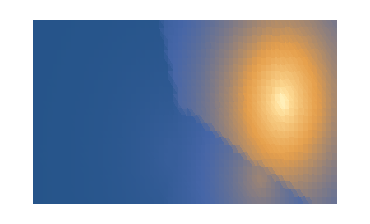

-Graphics-

```mathematica
(* Find nearest points towards the surface-tNow *) 

tNow=Ceiling@MaxTime+0;

precision=1;

tNowSurface=Flatten[Outer[{#1,#2,tNow}&,Range[xMin,xMax,precision],Range[yMin,yMax,precision]],1]; (* for step = 5 : size = 22*10 *)

nearestPtsIdx=Flatten[Nearest[ctsSelAllJλ[[All,1;;3]]->"Index"]/@tNowSurface,1];

nearestPtsCood=ctsSelAllJλ[[#,1;;3]]&/@nearestPtsIdx;
chosenλ=ctsSelAllJλ[[#,4;;5]]&/@nearestPtsIdx;
chosenCoef=ctsSelAllJλ[[#,6]]&/@nearestPtsIdx;

dist=MapThread[{f[#1[[1;;2]]-#2[[1;;2]]],Abs[#1[[3]]-#2[[3]]]}&,{tNowSurface,nearestPtsCood}];
pdfAdj=Exp@-MapThread[#1.#2&,{dist,chosenλ}];
pdfAdj=MapThread[#1*#2&,{pdfAdj,chosenCoef}];

valueSurface=ConstantArray[0,Dimensions@tNowSurface];
valueSurface[[All,1;;2]]=tNowSurface[[All,1;;2]];
valueSurface[[All,3]]=pdfAdj;

img2=ImageResize[img,{370,224}];
plot6=ListDensityPlot[valueSurface,AspectRatio->ImageAspectRatio@img2,PlotRangePadding->0,PlotRange->All,ImageSize->ImageDimensions[img2],Axes->False,Frame->None]
ImageAdd[ImageMultiply[plot6,0.5],ImageMultiply[img2,0.5]]
```